```mathematica
SetDirectory[NotebookDirectory[]]
rasterizeBackground[g_,res_: 100]:=Show[Graphics[{Inset[Rasterize[Show[g,ImagePadding->0,ImageMargins->0,LabelStyle->Opacity[0],FrameTicksStyle->Opacity[0],FrameStyle->Opacity[0],AxesStyle->Opacity[0],TicksStyle->Opacity[0],PlotRangeClipping->False],ImageResolution->res],Scaled[{0,0}],Scaled[{0,0}],Scaled[1]]}],Sequence@@Options[g],Sequence@@Options[g,PlotRange],Sequence@@Options[g,Epilog]];
```

/Users/zack/Documents/oscillators/faraday

## Single run plots

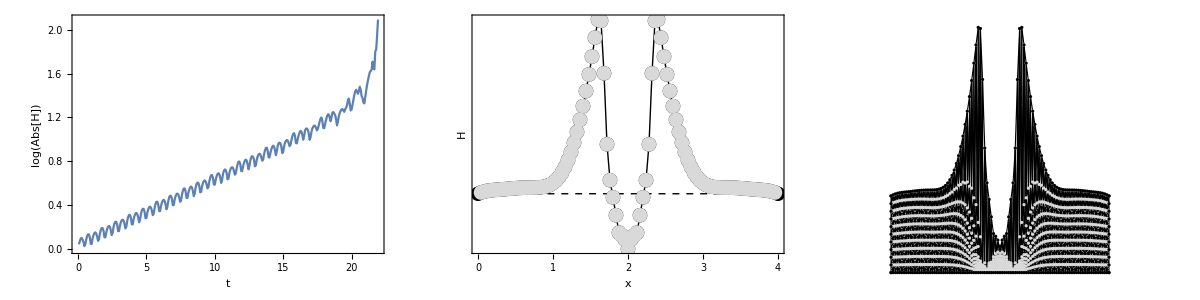

12.000000 0.500000

```mathematica
filebase="data/periodic";
lst=StringSplit[Import[filebase<>".txt"],"\n"];
meshpoints=ToExpression[lst[[FirstPosition[lst,"Mesh points"][[1]]+1]]];
mesh=Partition[Partition[BinaryReadList[filebase<>".npy","Real64"][[1+(10+BinaryReadList[filebase<>".npy","Integer16"][[5]])*8/64;;-1]],2],meshpoints];
norms=BinaryReadList[filebase<>"norms.npy","Real64"][[1+(10+BinaryReadList[filebase<>"norms.npy","Integer16"][[5]])*8/64;;-1]];
top=1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Surface points coordinates"][[1]]+1]]]];
top2=1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Interior surface points coordinates"][[1]]+1]]]];
length=ToExpression[lst[[FirstPosition[lst,"Length"][[1]]+1]]];
height=ToExpression[lst[[FirstPosition[lst,"Height"][[1]]+1]]];
bottom=1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Substrate points coordinates"][[1]]+1]]]];
con=Partition[1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Mesh cells"][[1]]+1]]," "]],3];
contop=Cases[con,u_/;Length[Intersection[top,u]]==2];
conbottom=Cases[con,u_/;Length[Intersection[bottom,u]]==2];
sides=Flatten[Position[mesh[[-1]],u_/;Length[u]>0&&(Abs[(u[[1]]^2)^(1/2)-length]<10^-6||Abs[(u[[1]]^2)^(1/2)]<10^-6)]];
m=Length[mesh];
mesh2=mesh[[m]];
Grid[{{ListPlot[Transpose[{Range[m]/15,Log[norms[[1;;m]]]/Log[10]}],Joined->True,PlotRange->All,ImageSize->350,ImagePadding->{{75,15},{75,15}},AspectRatio->1,Axes->False,Frame->True,FrameLabel->{t,Log[Abs[H]]},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2.0]]],Show[ListPlot[{SortBy[{#[[1]],#[[2]]-height}&/@mesh2[[top]],First],{{0,0},{length,0}}},FrameTicks->{Automatic,None},Joined->True,PlotRange->All,PlotStyle->{Directive[Black,AbsoluteThickness[1]],Directive[Black,Dashed,AbsoluteThickness[1]]},PlotRange->All,ImageSize->350,ImagePadding->{{75,15},{75,15}},AspectRatio->1,Axes->False,Frame->True,FrameLabel->{x,H},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2.0]]],ListPlot[{SortBy[{#[[1]],#[[2]]-height}&/@mesh2[[top]],First],{#[[1]],#[[2]]-height}&/@mesh2[[top2]]},FrameTicks->None,Joined->False,PlotStyle->{Directive[Black,PointSize[0.03]],Directive[LightGray,PointSize[0.03]]},PlotRange->All,ImageSize->350,ImagePadding->{{75,15},{75,15}},AspectRatio->1,Axes->False,Frame->True,FrameLabel->{x,H},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2.0]]]],
ListPlot[{mesh2,mesh2[[top]],mesh2[[sides]],mesh2[[bottom]]}, PlotStyle->{Directive[LightGray],Directive[Black],Directive[Black],Directive[Black]}, ImageSize->500,Axes->False,Frame->False,Prolog->{White,EdgeForm[Black],Triangle[{mesh2[[#[[1]]]],mesh2[[#[[2]]]],mesh2[[#[[3]]]]}]&/@con},AspectRatio->(Max[mesh[[m,All,2]]]-Min[mesh[[m,All,2]]])/(length+2),PlotRange->{{-1,length+1},{Min[mesh[[m,All,2]]],Max[mesh[[m,All,2]]]}}]}}]
lst[[-1]]
```

```mathematica
1.364372*980/(2*Pi*16.8)^2
```

0.12

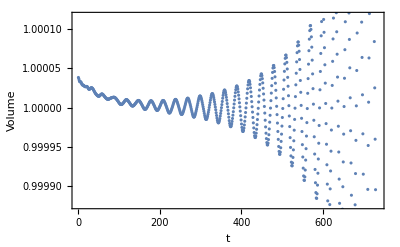

```mathematica
(* Numerical loss of fluid volume during saturation, but not too bad...*)
ListPlot[Total[#[[top,2]]]/(Length[top]*height)&/@mesh,Axes->False,Frame->True,FrameLabel->{t,"Volume"},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]]]
```

```mathematica
modes=Table[Pi*n/length,{n,1,20}]
frequencies=2*(980*modes*Tanh[height*modes]*(1+72/980*modes^2))^(1/2)/(2*Pi)
modes2=Table[Pi*n/length,{n,1,20}]
frequencies2=2*(980*modes2*Tanh[height*modes2]*(1+72/980*modes2^2))^(1/2)/(2*Pi)
```

{0.897598,1.7952,2.69279,3.59039,4.48799,5.38559,6.28319,7.18078,8.07838,8.97598,9.87358,10.7712,11.6688,12.5664,13.464,14.3616,15.2592,16.1568,17.0544,17.952}

{6.30357,12.5561,18.9171,25.6296,32.8713,40.7312,49.2379,58.3864,68.1559,78.52,89.4511,100.923,112.912,125.396,138.356,151.773,165.634,179.922,194.626,209.733}

{0.897598,1.7952,2.69279,3.59039,4.48799,5.38559,6.28319,7.18078,8.07838,8.97598,9.87358,10.7712,11.6688,12.5664,13.464,14.3616,15.2592,16.1568,17.0544,17.952}

{6.30357,12.5561,18.9171,25.6296,32.8713,40.7312,49.2379,58.3864,68.1559,78.52,89.4511,100.923,112.912,125.396,138.356,151.773,165.634,179.922,194.626,209.733}

## Generate box substrate

```mathematica
filebase="data/long";
lst=StringSplit[Import[filebase<>".txt"],"\n"];
meshpoints=ToExpression[lst[[FirstPosition[lst,"Mesh points"][[1]]+1]]];
mesh=Partition[Partition[BinaryReadList[filebase<>".npy","Real64"][[1+(10+BinaryReadList[filebase<>".npy","Integer16"][[5]])*8/64;;-1]],2],meshpoints];
top=1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Surface points coordinates"][[1]]+1]]]];
top2=1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Interior surface points coordinates"][[1]]+1]]]];
length=ToExpression[lst[[FirstPosition[lst,"Length"][[1]]+1]]];
height=ToExpression[lst[[FirstPosition[lst,"Height"][[1]]+1]]];
bottom=1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Substrate points coordinates"][[1]]+1]]]];
con=Partition[1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Mesh cells"][[1]]+1]]," "]],3];
contop=Cases[con,u_/;Length[Intersection[top,u]]==2];
conbottom=Cases[con,u_/;Length[Intersection[bottom,u]]==2];
sides=Flatten[Position[mesh[[-1]],u_/;Length[u]>0&&(Abs[(u[[1]]^2)^(1/2)-length]<10^-6||Abs[(u[[1]]^2)^(1/2)]<10^-6)]];
m=Length[mesh];
mesh2=mesh[[m]];
ListPlot[{mesh2,mesh2[[top]],mesh2[[sides]],mesh2[[bottom]]}, PlotStyle->{Directive[LightGray],Directive[Black],Directive[Black],Directive[Black]}, ImageSize->5000,Axes->False,Frame->False,Prolog->{White,EdgeForm[Black],Triangle[{mesh2[[#[[1]]]],mesh2[[#[[2]]]],mesh2[[#[[3]]]]}]&/@con},AspectRatio->(Max[mesh[[All,All,2]]]-Min[mesh[[All,All,2]]])/(length+2),PlotRange->{{-1,length+1},{Min[mesh[[All,All,2]]],Max[mesh[[All,All,2]]]}}]
```

```mathematica
modes=ToExpression[StringSplit[lst[[FirstPosition[lst,"Substrate modes"][[1]]+1]]]];
smodes=Length[modes]/2;
subss=ConstantArray[0.,{smodes,smodes}]
subsc=Normal[SparseArray[Table[{i,1}->modes[[i]],{i,1,smodes}],{smodes,smodes}]]
subcs=ConstantArray[0.,{smodes,smodes}]
subcc=Normal[SparseArray[Table[{i,1}->modes[[smodes+i]],{i,1,smodes}],{smodes,smodes}]]
file=OpenWrite["data/boxsubstrate.dat"]
WriteString[file,smodes]
WriteString[file,"\n"]
Do[Do[WriteString[file,subss[[j,i]]]; WriteString[file," "];,{i,1,smodes}];WriteString[file,"\n"],{j,1,smodes}]
WriteString[file,"\n"];
Do[Do[WriteString[file,subsc[[j,i]]]; WriteString[file," "];,{i,1,smodes}];WriteString[file,"\n"],{j,1,smodes}]
WriteString[file,"\n"];
Do[Do[WriteString[file,subcs[[j,i]]]; WriteString[file," "];,{i,1,smodes}];WriteString[file,"\n"],{j,1,smodes}]
WriteString[file,"\n"];
Do[Do[WriteString[file,subcc[[j,i]]]; WriteString[file," "];,{i,1,smodes}];WriteString[file,"\n"],{j,1,smodes}]
WriteString[file,"\n"];
Close[file]
```

{{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}}

{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

{{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}}

{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0.4,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

OutputStream[…]

data/boxsubstrate.dat

## Animation

```mathematica
m0=Length[mesh]-500;
m1=Length[mesh];
If[!DirectoryQ["rectangleanimation"],CreateDirectory["rectangleanimation"]];
Monitor[Do[
acc=ToExpression[StringSplit[lst[[-1]]," "]][[2]];
freq=ToExpression[StringSplit[lst[[-1]]," "]][[1]];
amp=980*acc/(2*Pi*freq)^2;
z0=amp*Sin[2*Pi*m/15];
mesh2={#[[1]],z0+#[[2]]}&/@mesh[[m]];
p=Grid[{{ListPlot[{Transpose[{Range[Length[norms]]/15,Log[norms]/Log[10]}],Transpose[{Range[m]/15,Log[norms[[1;;m]]]/Log[10]}]},Joined->True,PlotStyle->{Directive[AbsoluteThickness[1],LightGray],Directive[AbsoluteThickness[2],Black]},PlotRange->All,ImageSize->350,ImagePadding->{{75,15},{75,15}},AspectRatio->1,Axes->False,Frame->True,FrameLabel->{t,Log[Abs[H]]},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2.0]]],Show[ListPlot[{{#[[1]],#[[2]]-height}&/@mesh2[[top]]},FrameTicks->{Automatic,None},Joined->True,PlotRange->All,PlotStyle->{Directive[Black,AbsoluteThickness[1]]},PlotRange->All,ImageSize->350,ImagePadding->{{75,15},{75,15}},AspectRatio->1,Axes->False,Frame->True,FrameLabel->{x,H},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2.0]]],ListPlot[{{#[[1]],#[[2]]-height}&/@mesh2[[top]],{#[[1]],#[[2]]-height}&/@mesh2[[top2]]},FrameTicks->None,Joined->False,PlotStyle->{Directive[Black,PointSize[0.03]],Directive[LightGray,PointSize[0.03]]},PlotRange->All,ImageSize->350,ImagePadding->{{75,15},{75,15}},AspectRatio->1,Axes->False,Frame->True,FrameLabel->{x,H},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2.0]]]],
ListPlot[{mesh2,mesh2[[top]],mesh2[[sides]],mesh2[[bottom]]}, PlotStyle->{Directive[LightGray],Directive[Black],Directive[Black],Directive[Black]}, ImageSize->500,Axes->False,Frame->False,Prolog->{White,EdgeForm[Black],Triangle[{mesh2[[#[[1]]]],mesh2[[#[[2]]]],mesh2[[#[[3]]]]}]&/@con},AspectRatio->(height+2)/(length+2),PlotRange->{{-1,length+1},{-1,height+1}}]}}];
Export["rectangleanimation/"<>IntegerString[m-m0,10,4]<>".png",p,ImageResolution->100];,{m,m0,m1}],N[(m-m0)/(m1-m0)]]
```

```mathematica
Monitor[plots=Table[filebase="data/mode3";
lst=StringSplit[Import[filebase<>".txt"],"\n"];
meshpoints=ToExpression[lst[[FirstPosition[lst,"Mesh points"][[1]]+1]]];
mesh=Partition[Partition[BinaryReadList[filebase<>".npy","Real64"][[1+(10+BinaryReadList[filebase<>".npy","Integer16"][[5]])*8/64;;-1]],2],meshpoints];
acc=ToExpression[StringSplit[lst[[-1]]," "]][[2]];
freq=ToExpression[StringSplit[lst[[-1]]," "]][[1]];
amp=980*acc/(2*Pi*freq)^2;
z0=amp*Sin[2*Pi*m/15];
norms=BinaryReadList[filebase<>"norms.npy","Real64"][[1+(10+BinaryReadList[filebase<>"norms.npy","Integer16"][[5]])*8/64;;-1]];
top=1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Surface points coordinates"][[1]]+1]]]];
top2=1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Interior surface points coordinates"][[1]]+1]]]];
length=ToExpression[lst[[FirstPosition[lst,"Length"][[1]]+1]]];
height=ToExpression[lst[[FirstPosition[lst,"Height"][[1]]+1]]];
bottom=1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Substrate points coordinates"][[1]]+1]]]];
con=Partition[1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Mesh cells"][[1]]+1]]," "]],3];
contop=Cases[con,u_/;Length[Intersection[top,u]]==2];
conbottom=Cases[con,u_/;Length[Intersection[bottom,u]]==2];
sides=Flatten[Position[mesh[[-1]],u_/;Length[u]>0&&(Abs[(u[[1]]^2)^(1/2)-length]<10^-6||Abs[(u[[1]]^2)^(1/2)]<10^-6)]];
mesh2={#[[1]],z0+#[[2]]}&/@mesh[[m]];
p1=Show[ListPlot[{mesh2[[top]]}, PlotStyle->Directive[Black],Joined->True, ImageSize->300,Axes->False,Frame->False,Prolog->{White,EdgeForm[Directive[Blue,AbsoluteThickness[0.1]]],Triangle[{mesh2[[#[[1]]]],mesh2[[#[[2]]]],mesh2[[#[[3]]]]}]&/@con},AspectRatio->(1.5)/(length+2),PlotRange->{{-1,length+1},{-0.75,0.75}}],ListPlot[mesh2[[bottom]],Joined->True,PlotStyle->{Directive[ColorData[97,"ColorList"][[1]],AbsoluteThickness[2]]}]],{m,1,Length[mesh]-0}];,N[m/Length[mesh]]]
CreateDirectory[filebase<>"animation"];AbsoluteTiming[Monitor[Do[Export[filebase<>"animation/"<>IntegerString[m,10,4]<>".png",plots[[m]],ImageResolution->200],{m,1,Length[plots],1}],N[m/Length[plots]]]]
```

CreateDirectory::filex: /Users/zack/Documents/oscillators/faraday/data/mode3animation already exists.

{249.84,Null}

## Periodic sweep plots

sweeps/randomacc

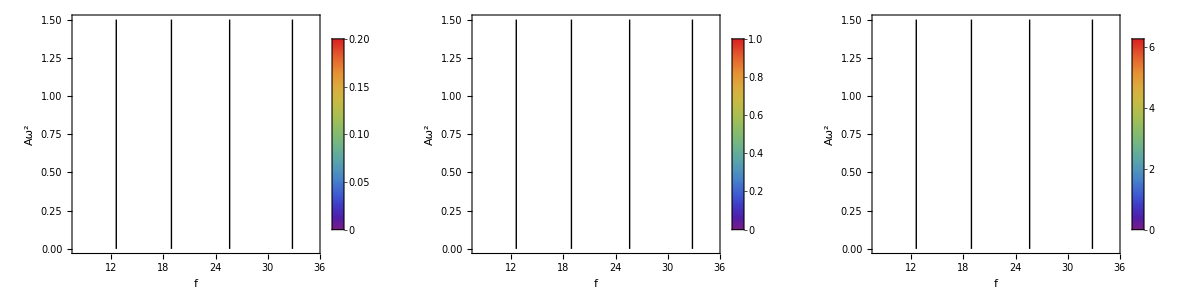

```mathematica
filebase="sweeps/randomacc"
growth1=Flatten[Table[If[FileExistsQ[filebase<>"/params"<>ToString[i]<>".txt"],Internal`StringToDouble/@#&/@DeleteCases[StringSplit/@StringSplit[Import[filebase<>"/params"<>ToString[i]<>".txt"],"\n"],{}],{}],{i,1,100}],1];
Amin=Min[growth1[[All,2]]];
Amax=Max[growth1[[All,2]]];
fmin=Min[growth1[[All,1]]];
fmax=Max[growth1[[All,1]]];
kmin=0;
kmax=2*Pi;
max=Max[growth1[[All,4]]];
ν1=0.5;
ν2=0;
ν3=0.1;
g=980;
σ=50;
length=3.5;
p1=Grid[{{Show[rasterizeBackground[Show[ListDensityPlot[growth1[[All,{1,2,4}]],InterpolationOrder->0,PlotRange->{All,All,{0.0,max}},ClippingStyle->None,LabelStyle->Directive[16,Black],ColorFunction->(ColorData["Rainbow"][#/max]&),ColorFunctionScaling->False, FrameLabel->{{Aω^2,None},{f,"Growth Rate"}},Epilog->{Inset[BarLegend[{"Rainbow",{0,0.2}},LabelStyle->Directive[16,Black]],Scaled[{1.2,0.5}]],Line[{{#,Amin},{#,Amax}}]&/@Cases[frequencies,u_/;u>fmin&&u<fmax]}],Plot[2*(ν1+ν3*k^2+ν2*k*Tanh[k*height])*(1+σ/g*k^2)/(k*Tanh[k*height]*(g+σ*k^2))^(1/2)/.FindRoot[2*Pi*f/2==(k*Tanh[k*height]*(g+σ*k^2))^(1/2), {k,1.0}],{f,fmin,fmax},PlotStyle->Directive[Black]]]],Epilog->{Inset[BarLegend[{"Rainbow",{0,0.2}},LabelStyle->Directive[16,Black]],Scaled[{1.2,0.5}]],Line[{{#,Amin},{#,Amax}}]&/@Cases[frequencies,u_/;u>fmin&&u<fmax]},PlotRangeClipping->False,ImageSize->400,ImagePadding->{{65,100},{50,50}}],rasterizeBackground[Show[ListDensityPlot[ReplacePart[growth1[[All,{1,2,3}]],Position[growth1[[All,{1,2,4}]],u_/;u<0]->-1],InterpolationOrder->0,PlotRange->{All,All,{0.0,1.1}},ClippingStyle->None,LabelStyle->Directive[16,Black],ColorFunction->(ColorData["Rainbow"][#/1.0]&),ColorFunctionScaling->False,FrameLabel->{{Aω^2,None},{f,"Frequency"}},ImageSize->300],PlotRangeClipping->None,Epilog->{Inset[BarLegend[{"Rainbow",{0,1}},LabelStyle->Directive[16,Black]],Scaled[{1.2,0.5}]],Line[{{#,Amin},{#,Amax}}]&/@Cases[frequencies,u_/;u>fmin&&u<fmax]},ImageSize->400,ImagePadding->{{65,100},{50,50}}]],rasterizeBackground[Show[ListDensityPlot[ReplacePart[growth1[[All,{1,2,5}]],Position[growth1[[All,{1,2,4}]],u_/;u<0]->-1],InterpolationOrder->0,PlotRange->{All,All,{kmin-0.01,kmax+0.01}},ClippingStyle->None,LabelStyle->Directive[16,Black],ColorFunction->(ColorData["Rainbow"][(#-kmin)/(kmax-kmin)]&),ColorFunctionScaling->False, FrameLabel->{{Aω^2,None},{f,"Wave number"}}],PlotRangeClipping->None,Epilog->{Inset[BarLegend[{"Rainbow",{kmin,kmax}},LabelStyle->Directive[16,Black]],Scaled[{1.2,0.5}]],Line[{{#,Amin},{#,Amax}}]&/@Cases[frequencies,u_/;u>fmin&&u<fmax]},ImageSize->400,ImagePadding->{{65,100},{50,50}}]]}}]
```

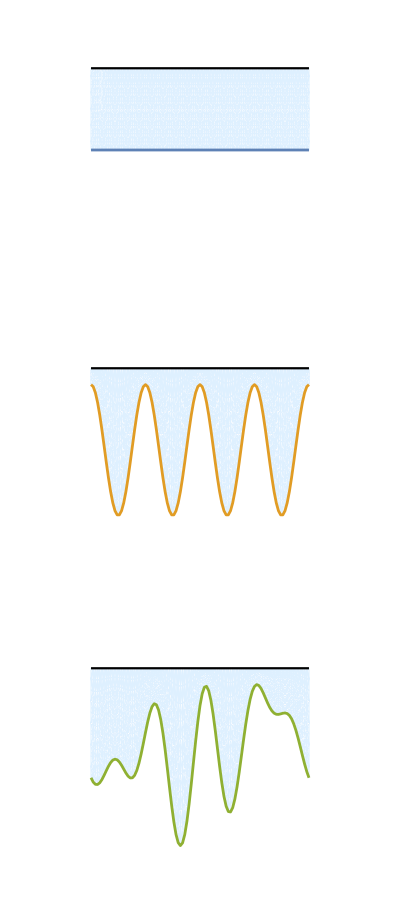

plots/substrates.pdf

```mathematica
filebase="data/flat";
lst=StringSplit[Import[filebase<>".txt"],"\n"];
meshpoints=ToExpression[lst[[FirstPosition[lst,"Mesh points"][[1]]+1]]];
mesh=Partition[Partition[BinaryReadList[filebase<>".npy","Real64"][[1+(10+BinaryReadList[filebase<>".npy","Integer16"][[5]])*8/64;;-1]],2],meshpoints];
norms=BinaryReadList[filebase<>"norms.npy","Real64"][[1+(10+BinaryReadList[filebase<>"norms.npy","Integer16"][[5]])*8/64;;-1]];
top=1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Surface points coordinates"][[1]]+1]]]];
top2=1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Interior surface points coordinates"][[1]]+1]]]];
length=ToExpression[lst[[FirstPosition[lst,"Length"][[1]]+1]]];
height=ToExpression[lst[[FirstPosition[lst,"Height"][[1]]+1]]];
bottom=1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Substrate points coordinates"][[1]]+1]]]];
con=Partition[1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Mesh cells"][[1]]+1]]," "]],3];
contop=Cases[con,u_/;Length[Intersection[top,u]]==2];
conbottom=Cases[con,u_/;Length[Intersection[bottom,u]]==2];
sides=Flatten[Position[mesh[[-1]],u_/;Length[u]>0&&(Abs[(u[[1]]^2)^(1/2)-length]<10^-6||Abs[(u[[1]]^2)^(1/2)]<10^-6)]];
m=1;
mesh2=mesh[[m]];
p1=Show[ListPlot[{mesh2[[top]]}, PlotStyle->Directive[Black],Joined->True, ImageSize->300,Axes->False,Frame->False,Prolog->{White,EdgeForm[LightBlue],Triangle[{mesh2[[#[[1]]]],mesh2[[#[[2]]]],mesh2[[#[[3]]]]}]&/@con},AspectRatio->(1.5)/(length+2),PlotRange->{{-1,length+1},{-0.75,0.75}}],ListPlot[mesh2[[bottom]],Joined->True,PlotStyle->{Directive[ColorData[97,"ColorList"][[1]],AbsoluteThickness[2]]}]];
filebase="data/periodic";
lst=StringSplit[Import[filebase<>".txt"],"\n"];
meshpoints=ToExpression[lst[[FirstPosition[lst,"Mesh points"][[1]]+1]]];
mesh=Partition[Partition[BinaryReadList[filebase<>".npy","Real64"][[1+(10+BinaryReadList[filebase<>".npy","Integer16"][[5]])*8/64;;-1]],2],meshpoints];
norms=BinaryReadList[filebase<>"norms.npy","Real64"][[1+(10+BinaryReadList[filebase<>"norms.npy","Integer16"][[5]])*8/64;;-1]];
top=1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Surface points coordinates"][[1]]+1]]]];
top2=1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Interior surface points coordinates"][[1]]+1]]]];
length=ToExpression[lst[[FirstPosition[lst,"Length"][[1]]+1]]];
height=ToExpression[lst[[FirstPosition[lst,"Height"][[1]]+1]]];
bottom=1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Substrate points coordinates"][[1]]+1]]]];
con=Partition[1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Mesh cells"][[1]]+1]]," "]],3];
contop=Cases[con,u_/;Length[Intersection[top,u]]==2];
conbottom=Cases[con,u_/;Length[Intersection[bottom,u]]==2];
sides=Flatten[Position[mesh[[-1]],u_/;Length[u]>0&&(Abs[(u[[1]]^2)^(1/2)-length]<10^-6||Abs[(u[[1]]^2)^(1/2)]<10^-6)]];
m=1;
mesh2=mesh[[m]];
p2=Show[ListPlot[{mesh2[[top]]}, PlotStyle->Directive[Black],Joined->True, ImageSize->300,Axes->False,Frame->False,Prolog->{White,EdgeForm[LightBlue],Triangle[{mesh2[[#[[1]]]],mesh2[[#[[2]]]],mesh2[[#[[3]]]]}]&/@con},AspectRatio->(1.5)/(length+2),PlotRange->{{-1,length+1},{-0.75,0.75}}],ListPlot[mesh2[[bottom]],Joined->True,PlotStyle->{Directive[ColorData[97,"ColorList"][[2]],AbsoluteThickness[2]]}]];
filebase="data/random";
lst=StringSplit[Import[filebase<>".txt"],"\n"];
meshpoints=ToExpression[lst[[FirstPosition[lst,"Mesh points"][[1]]+1]]];
mesh=Partition[Partition[BinaryReadList[filebase<>".npy","Real64"][[1+(10+BinaryReadList[filebase<>".npy","Integer16"][[5]])*8/64;;-1]],2],meshpoints];
norms=BinaryReadList[filebase<>"norms.npy","Real64"][[1+(10+BinaryReadList[filebase<>"norms.npy","Integer16"][[5]])*8/64;;-1]];
top=1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Surface points coordinates"][[1]]+1]]]];
top2=1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Interior surface points coordinates"][[1]]+1]]]];
length=ToExpression[lst[[FirstPosition[lst,"Length"][[1]]+1]]];
height=ToExpression[lst[[FirstPosition[lst,"Height"][[1]]+1]]];
bottom=1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Substrate points coordinates"][[1]]+1]]]];
con=Partition[1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Mesh cells"][[1]]+1]]," "]],3];
contop=Cases[con,u_/;Length[Intersection[top,u]]==2];
conbottom=Cases[con,u_/;Length[Intersection[bottom,u]]==2];
sides=Flatten[Position[mesh[[-1]],u_/;Length[u]>0&&(Abs[(u[[1]]^2)^(1/2)-length]<10^-6||Abs[(u[[1]]^2)^(1/2)]<10^-6)]];
m=1;
mesh2=mesh[[m]];
p3=Show[ListPlot[{mesh2[[top]]}, PlotStyle->Directive[Black], Joined->True,ImageSize->300,Axes->False,Frame->False,Prolog->{White,EdgeForm[LightBlue],Triangle[{mesh2[[#[[1]]]],mesh2[[#[[2]]]],mesh2[[#[[3]]]]}]&/@con},AspectRatio->(1.5)/(length+2),PlotRange->{{-1,length+1},{-0.75,0.75}}],ListPlot[mesh2[[bottom]],Joined->True,PlotStyle->{Directive[ColorData[97,"ColorList"][[3]],AbsoluteThickness[2]]}]];

p0=Grid[{{p1},{p2},{p3}}]
Export["plots/substrates.pdf",p0]
```

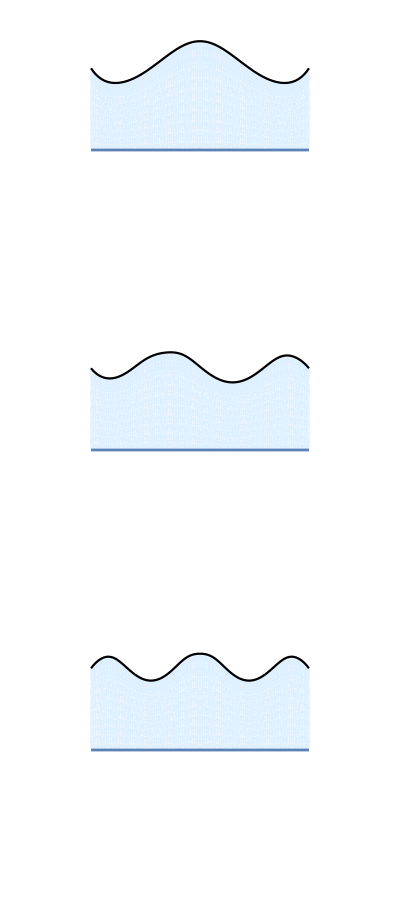

plots/modes.pdf

```mathematica
filebase="data/mode1";
lst=StringSplit[Import[filebase<>".txt"],"\n"];
meshpoints=ToExpression[lst[[FirstPosition[lst,"Mesh points"][[1]]+1]]];
mesh=Partition[Partition[BinaryReadList[filebase<>".npy","Real64"][[1+(10+BinaryReadList[filebase<>".npy","Integer16"][[5]])*8/64;;-1]],2],meshpoints];
norms=BinaryReadList[filebase<>"norms.npy","Real64"][[1+(10+BinaryReadList[filebase<>"norms.npy","Integer16"][[5]])*8/64;;-1]];
top=1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Surface points coordinates"][[1]]+1]]]];
top2=1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Interior surface points coordinates"][[1]]+1]]]];
length=ToExpression[lst[[FirstPosition[lst,"Length"][[1]]+1]]];
height=ToExpression[lst[[FirstPosition[lst,"Height"][[1]]+1]]];
bottom=1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Substrate points coordinates"][[1]]+1]]]];
con=Partition[1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Mesh cells"][[1]]+1]]," "]],3];
contop=Cases[con,u_/;Length[Intersection[top,u]]==2];
conbottom=Cases[con,u_/;Length[Intersection[bottom,u]]==2];
sides=Flatten[Position[mesh[[-1]],u_/;Length[u]>0&&(Abs[(u[[1]]^2)^(1/2)-length]<10^-6||Abs[(u[[1]]^2)^(1/2)]<10^-6)]];
m=Length[mesh]-95;
mesh2=mesh[[m]];
p1=Show[ListPlot[{mesh2[[top]]}, PlotStyle->Directive[Black],Joined->True, ImageSize->300,Axes->False,Frame->False,Prolog->{White,EdgeForm[LightBlue],Triangle[{mesh2[[#[[1]]]],mesh2[[#[[2]]]],mesh2[[#[[3]]]]}]&/@con},AspectRatio->(1.5)/(length+2),PlotRange->{{-1,length+1},{-0.75,0.75}}],ListPlot[mesh2[[bottom]],Joined->True,PlotStyle->{Directive[ColorData[97,"ColorList"][[1]],AbsoluteThickness[2]]}]];
filebase="data/mode2";
lst=StringSplit[Import[filebase<>".txt"],"\n"];
meshpoints=ToExpression[lst[[FirstPosition[lst,"Mesh points"][[1]]+1]]];
mesh=Partition[Partition[BinaryReadList[filebase<>".npy","Real64"][[1+(10+BinaryReadList[filebase<>".npy","Integer16"][[5]])*8/64;;-1]],2],meshpoints];
norms=BinaryReadList[filebase<>"norms.npy","Real64"][[1+(10+BinaryReadList[filebase<>"norms.npy","Integer16"][[5]])*8/64;;-1]];
top=1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Surface points coordinates"][[1]]+1]]]];
top2=1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Interior surface points coordinates"][[1]]+1]]]];
length=ToExpression[lst[[FirstPosition[lst,"Length"][[1]]+1]]];
height=ToExpression[lst[[FirstPosition[lst,"Height"][[1]]+1]]];
bottom=1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Substrate points coordinates"][[1]]+1]]]];
con=Partition[1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Mesh cells"][[1]]+1]]," "]],3];
contop=Cases[con,u_/;Length[Intersection[top,u]]==2];
conbottom=Cases[con,u_/;Length[Intersection[bottom,u]]==2];
sides=Flatten[Position[mesh[[-1]],u_/;Length[u]>0&&(Abs[(u[[1]]^2)^(1/2)-length]<10^-6||Abs[(u[[1]]^2)^(1/2)]<10^-6)]];
m=Length[mesh]-87;
mesh2=mesh[[m]];
p2=Show[ListPlot[{mesh2[[top]]}, PlotStyle->Directive[Black],Joined->True, ImageSize->300,Axes->False,Frame->False,Prolog->{White,EdgeForm[LightBlue],Triangle[{mesh2[[#[[1]]]],mesh2[[#[[2]]]],mesh2[[#[[3]]]]}]&/@con},AspectRatio->(1.5)/(length+2),PlotRange->{{-1,length+1},{-0.75,0.75}}],ListPlot[mesh2[[bottom]],Joined->True,PlotStyle->{Directive[ColorData[97,"ColorList"][[1]],AbsoluteThickness[2]]}]];
filebase="data/mode3";
lst=StringSplit[Import[filebase<>".txt"],"\n"];
meshpoints=ToExpression[lst[[FirstPosition[lst,"Mesh points"][[1]]+1]]];
mesh=Partition[Partition[BinaryReadList[filebase<>".npy","Real64"][[1+(10+BinaryReadList[filebase<>".npy","Integer16"][[5]])*8/64;;-1]],2],meshpoints];
norms=BinaryReadList[filebase<>"norms.npy","Real64"][[1+(10+BinaryReadList[filebase<>"norms.npy","Integer16"][[5]])*8/64;;-1]];
top=1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Surface points coordinates"][[1]]+1]]]];
top2=1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Interior surface points coordinates"][[1]]+1]]]];
length=ToExpression[lst[[FirstPosition[lst,"Length"][[1]]+1]]];
height=ToExpression[lst[[FirstPosition[lst,"Height"][[1]]+1]]];
bottom=1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Substrate points coordinates"][[1]]+1]]]];
con=Partition[1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Mesh cells"][[1]]+1]]," "]],3];
contop=Cases[con,u_/;Length[Intersection[top,u]]==2];
conbottom=Cases[con,u_/;Length[Intersection[bottom,u]]==2];
sides=Flatten[Position[mesh[[-1]],u_/;Length[u]>0&&(Abs[(u[[1]]^2)^(1/2)-length]<10^-6||Abs[(u[[1]]^2)^(1/2)]<10^-6)]];
m=Length[mesh]-100;
mesh2=mesh[[m]];
p3=Show[ListPlot[{mesh2[[top]]}, PlotStyle->Directive[Black], Joined->True,ImageSize->300,Axes->False,Frame->False,Prolog->{White,EdgeForm[LightBlue],Triangle[{mesh2[[#[[1]]]],mesh2[[#[[2]]]],mesh2[[#[[3]]]]}]&/@con},AspectRatio->(1.5)/(length+2),PlotRange->{{-1,length+1},{-0.75,0.75}}],ListPlot[mesh2[[bottom]],Joined->True,PlotStyle->{Directive[ColorData[97,"ColorList"][[1]],AbsoluteThickness[2]]}]];

p0=Grid[{{p1},{p2},{p3}}]
Export["plots/modes.pdf",p0]
```

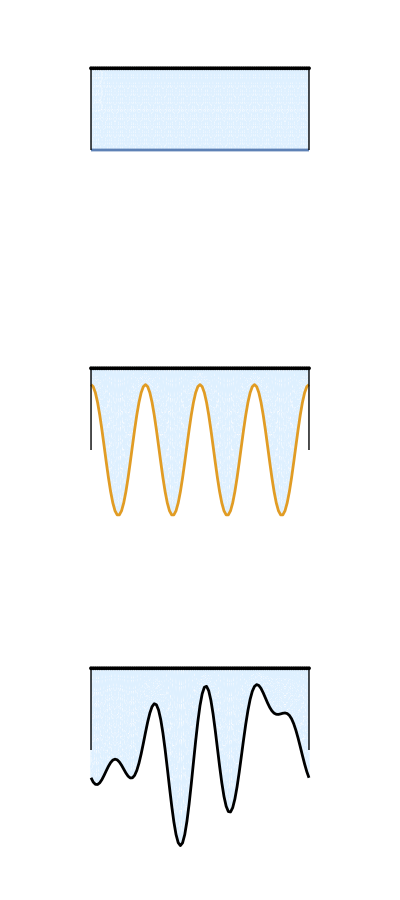
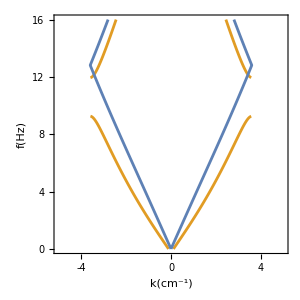
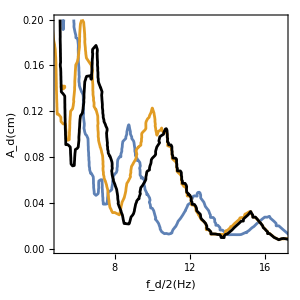
-Graphics- | -Graphics- | -Graphics-

plots/periodicrectanglegap.pdf

```mathematica
height=0.5;
length=3.5;
gap=2*Pi/length*4/2;
ks=2*gap;
hs=0.4;
M2=4;
κ[k_, n_]:=k+n*ks;
ν1=2;
ν3=0.1;
g=980;
σ=72;
ρ=1;
H1[k_,A_]:=Table[Exp[-κ[k,n]*height]*(g+σ/ρ*κ[k,n]^2)*κ[k,n]*(BesselJ[m-n,-I*κ[k,n]*A]-I/2*ks*A*BesselJ[m-n-1,-I*κ[k,n]*A]-I/2*ks*A*BesselJ[m-n+1,-I*κ[k,n]*A])-Exp[κ[k,n]*height]*(g+σ/ρ*κ[k,n]^2)*κ[k,n]*(BesselJ[m-n,I*κ[k,n]*A]+I/2*ks*A*BesselJ[m-n-1,I*κ[k,n]*A]+I/2*ks*A*BesselJ[m-n+1,I*κ[k,n]*A]),{n,-M2,M2},{m,-M2,M2}];
H2[k_,A_]:=-Table[Exp[-κ[k,n]*height]*(BesselJ[m-n,-I*κ[k,n]*A]-I/2*ks*A*BesselJ[m-n-1,-I*κ[k,n]*A]-I/2*ks*A*BesselJ[m-n+1,-I*κ[k,n]*A])+Exp[κ[k,n]*height]*(BesselJ[m-n,I*κ[k,n]*A]+I/2*ks*A*BesselJ[m-n-1,I*κ[k,n]*A]+I/2*ks*A*BesselJ[m-n+1,I*κ[k,n]*A]),{n,-M2,M2},{m,-M2,M2}];
H3[k_,A_]:=Table[1.0/Cosh[κ[k,n]*height]*KroneckerDelta[n,m],{n,-M2,M2},{m,-M2,M2}];
sys[k_,A_]:={H3[k,A].H1[k,A],H3[k,A].H2[k,A]};
p1=Show[ListPlot[Transpose[Table[{k,#^(1/2)/(2*Pi)-0.25}&/@SingularValueList[sys[k,hs]][[-3;;-1]],{k,-ks/2+0.01,ks/2-0.01,ks/200}]],Joined->True,Axes->False,Frame->True,LabelStyle->Directive[16],PlotRange->{{-5,5},{0,16}},FrameTicks->{{Table[{i,i},{i,0,16,4}],Table[{i,""},{i,4,14,2}]},{Table[{i,i},{i,-4,4,2}],Table[{i,""},{i,-4,4,2}]}},FrameLabel->{DisplayForm[RowBox[{k,"(",Superscript["cm",-1],")"}]],DisplayForm[RowBox[{f,"(Hz)"}]]},FrameStyle->Directive[Black,AbsoluteThickness[2]],AspectRatio->1,ImageSize->300,ImagePadding->{{65,10},{65,10}},LabelStyle->Directive[16],PlotRange->{{-2.5,2.5},{0,16}},PlotStyle->Directive[AbsoluteThickness[2],ColorData[97,"ColorList"][[2]]]],ListPlot[{Table[{If[k<gap,k,If[k<3*gap,2*gap-k,k-4*gap]],(g*k*Tanh[k*height]*(1+σ/g*k^2))^(1/2)/(2*Pi)},{k,0,6*Pi/length,Pi/length/50}],Table[{-If[k<gap,k,If[k<3*gap,2*gap-k,k-4*gap]],(g*k*Tanh[k*height]*(1+σ/g*k^2))^(1/2)/(2*Pi)},{k,0,6*Pi/length,Pi/length/50}]},Joined->True,Axes->False,Frame->True,FrameStyle->Directive[Black,AbsoluteThickness[2.0]],PlotStyle->Directive[ColorData[97,"ColorList"][[1]],AbsoluteThickness[2.0]],AspectRatio->1,ImageSize->300,ImagePadding->{{65,10},{65,10}},LabelStyle->Directive[16],PlotRange->{{-2.5,2.5},{0,16}},FrameTicks->{{Table[{i,i},{i,0,16,4}],Table[{i,""},{i,4,14,2}]},{Table[{i,i},{i,-4,4,2}],Table[{i,""},{i,-4,4,2}]}},FrameLabel->{DisplayForm[RowBox[{k,"(",Superscript["cm",-1],")"}]],DisplayForm[RowBox[{f,"(Hz)"}]]},RotateLabel->True]];
filebases={"sweeps/flat2amp","sweeps/periodic2amp","sweeps/random2amp"};
sweeps=Flatten[Table[If[FileExistsQ[#<>"/params"<>ToString[i]<>".txt"],Internal`StringToDouble/@#&/@DeleteCases[StringSplit/@StringSplit[Import[#<>"/params"<>ToString[i]<>".txt"],"\n"],{}],{}],{i,1,100}],1]&/@filebases;
interpolations[f_,a_]=Table[Interpolation[{#[[1]]/2,#[[2]]/(2*Pi*#[[1]])^2*980,#[[3]]}&/@sweeps[[i,All,{1,2,4}]],InterpolationOrder->1][f,a],{i,1,Length[sweeps]}];cols={ColorData[97,"ColorList"][[1]],ColorData[97,"ColorList"][[2]],Black};p3=Show@@Table[ListContourPlot[{#[[1]]/2,#[[2]]/(2*Pi*#[[1]])^2*980,#[[3]]}&/@sweeps[[i,All,{1,2,4}]],Contours->{0.0},PlotRange->{{5,17},{0,0.2}},ContourShading->None,ContourStyle->{Directive[cols[[i]],Opacity[1],AbsoluteThickness[2]]},LabelStyle->Directive[16,Black],ColorFunction->(ColorData["Rainbow"][#/max]&),ColorFunctionScaling->False, FrameLabel->{{DisplayForm[RowBox[{HoldForm[Subscript[A,d]],"(cm)"}]],None},{DisplayForm[RowBox[{Subscript[f,d],"/",2,"(Hz)"}]],None}},FrameStyle->Directive[Black,AbsoluteThickness[2.0]],ImageSize->300,ImagePadding->{{65,10},{65,10}},FrameTicks->{{Table[{i,PaddedForm[i,{2,2}]},{i,0,0.2,0.04}],Table[{i,""},{i,0,0.2,0.04}]},{Table[{i,i},{i,4,16,2}],Table[{i,""},{i,4,16,2}]}}],{i,1,Length[sweeps]}];
p=Grid[{{p0,p1,p3}}]
Export["plots/periodicrectanglegap.pdf",p]
```

```mathematica
filebases={"sweeps/flat2acc","sweeps/periodic2acc","sweeps/random2acc"};
sweeps=Flatten[Table[If[FileExistsQ[#<>"/params"<>ToString[i]<>".txt"],Internal`StringToDouble/@#&/@DeleteCases[StringSplit/@StringSplit[Import[#<>"/params"<>ToString[i]<>".txt"],"\n"],{}],{}],{i,1,100}],1]&/@filebases;
Amin=Min[sweeps[[1,All,2]]];
Amax=Max[sweeps[[1,All,2]]];
fmin=Min[sweeps[[1,All,1]]];
fmax=Max[sweeps[[1,All,1]]];
kmin=Min[sweeps[[1,All,5]]];
kmax=Max[sweeps[[1,All,5]]];
max=Max[sweeps[[1,All,4]]];
p1=Table[rasterizeBackground[ListDensityPlot[{#[[1]],#[[2]],#[[3]]}&/@ReplacePart[sweeps[[i,All,{1,2,5}]],Position[sweeps[[i,All,{1,2,4}]],u_/;u<0]->-1],InterpolationOrder->0,PlotRange->{All,All,{kmin-0.01,kmax+0.01}},ClippingStyle->None,LabelStyle->Directive[16,Black],ColorFunction->(ColorData["Rainbow"][(#-kmin)/(kmax-kmin)]&),ColorFunctionScaling->False, FrameLabel->{{Aω^2,None},{f,"Wave number"}},PlotRangeClipping->None,Prolog->{AbsoluteThickness[1],Line[{{1/2*#,Amin},{1/2*#,Amax}}]&/@Cases[frequencies2,u_/;u>fmin&&u<fmax],Dashed,Line[{{1/2*#,Amin},{1/2*#,Amax}}]&/@Cases[frequencies2/2,u_/;u>fmin&&u<fmax&&u<Min[frequencies]*0.75]},Epilog->{Inset[BarLegend[{"Rainbow",{kmin,kmax}},LabelStyle->Directive[16,Black]],Scaled[{1.2,0.5}]]},ImageSize->400,ImagePadding->{{65,100},{50,50}}]],{i,1,Length[sweeps]}];
p=Grid[{p1}]
Export["plots/modes.pdf",p]
```

-Graphics- | -Graphics- | -Graphics-

plots/modes.pdf

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885]}

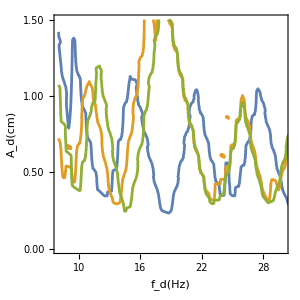

plots/ref.pdf

```mathematica
cols={ColorData[97,"ColorList"][[1]],ColorData[97,"ColorList"][[2]],ColorData[97,"ColorList"][[3]]}
filebases={"sweeps/flatacc","sweeps/periodicacc","sweeps/randomacc"};
sweeps=Flatten[Table[If[FileExistsQ[#<>"/params"<>ToString[i]<>".txt"],Internal`StringToDouble/@#&/@DeleteCases[StringSplit/@StringSplit[Import[#<>"/params"<>ToString[i]<>".txt"],"\n"],{}],{}],{i,1,100}],1]&/@filebases;
p=Show@@Table[ListContourPlot[{#[[1]],#[[2]],#[[3]]}&/@sweeps[[i,All,{1,2,4}]],Contours->{0.0},PlotRange->{{8,30},{0,1.5}},ContourShading->None,ContourStyle->{Directive[cols[[i]],Opacity[1],AbsoluteThickness[2]]},LabelStyle->Directive[16,Black],ColorFunctionScaling->False, FrameLabel->{{DisplayForm[RowBox[{HoldForm[Subscript[A,d]],"(cm)"}]],None},{DisplayForm[RowBox[{Subscript[f,d],"(Hz)"}]],None}},FrameStyle->Directive[Black,AbsoluteThickness[2.0]],ImageSize->300,ImagePadding->{{65,10},{65,10}},FrameTicks->{{Table[{i,PaddedForm[i,{2,2}]},{i,0,1.5,0.5}],Table[{i,""},{i,0,1.5,0.5}]},{Table[{i,i},{i,10,30,2}],Table[{i,""},{i,10,30,2}]}}],{i,1,Length[sweeps]}]
Export["plots/ref.pdf",p]
```

## Random substrates

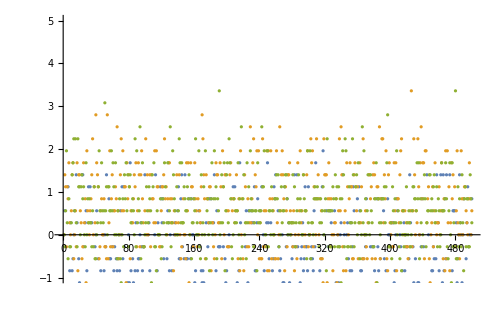

{480.,191.,51.,397.,218.,131.,94.,366.,243.,354.}

{426.,54.,170.,40.,229.,66.,438.,387.,340.,265.}

{229.,124.,299.,468.,142.,191.,131.,261.,244.,88.}

{4.2,3.36,6.44}

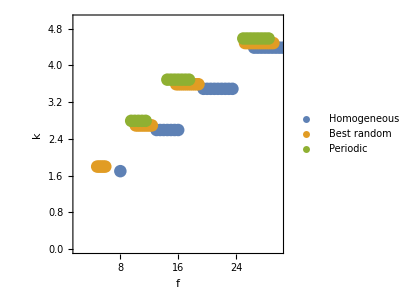

```mathematica
filebases={"sweeps/flat2acc","sweeps/periodic2acc"};
sweeps=Flatten[Table[If[FileExistsQ[#<>"/params"<>ToString[i]<>".txt"],Internal`StringToDouble/@#&/@DeleteCases[StringSplit/@StringSplit[Import[#<>"/params"<>ToString[i]<>".txt"],"\n"],{}],{}],{i,1,56}],1]&/@filebases;
filebase=cd;
random=DeleteCases[Table[If[FileExistsQ[filebase<>"/params"<>ToString[i]<>".txt"],Internal`StringToDouble/@#&/@DeleteCases[StringSplit/@StringSplit[Import[filebase<>"/params"<>ToString[i]<>".txt"],"\n"],{}],{}],{i,1,500}],{}];
seeds=Flatten[DeleteDuplicates/@random[[All,All,7]]];
wavenumbers=Sort[DeleteDuplicates[Flatten[(Cases[#,u_/;u[[4]]>0.0&&u[[3]]<0.6]&/@random)[[All,All,5]]]]];
means[case_]:=Mean/@(Cases[#,u_/;u[[4]]>0.0&&u[[3]]<0.6&&u[[5]]==case]&/@random)[[All,All,1]]
gaps=(means/@wavenumbers[[2;;4]])-(means/@wavenumbers[[1;;3]]);
mins[case_]:=Min/@(Cases[#,u_/;u[[4]]>0.0&&u[[3]]<0.6&&u[[5]]==case]&/@random)[[All,All,1]]
maxes[case_]:=Max/@(Cases[#,u_/;u[[4]]>0.0&&u[[3]]<0.6&&u[[5]]==case]&/@random)[[All,All,1]]
gaps=(mins/@wavenumbers[[2;;-1]])-(maxes/@wavenumbers[[1;;-2]]);
shifts=Transpose[#-gaps[[All,1]]&/@(Transpose[gaps])];
ListPlot[shifts,ImageSize->500,PlotRange->{-1,5}]
DeleteCases[Reverse[SortBy[seeds,shifts[[3,First@FirstPosition[seeds,#]]]&]],u_/;MemberQ[Position[gaps,Mean[{}]][[All,2]],Round[u]]][[1;;10]]
DeleteCases[Reverse[SortBy[seeds,shifts[[2,First@FirstPosition[seeds,#]]]&]],u_/;MemberQ[Position[gaps,Mean[{}]][[All,2]],Round[u]]][[1;;10]]
DeleteCases[Reverse[SortBy[seeds,Mean[shifts[[2;;3,First@FirstPosition[seeds,#]]]]&]],u_/;MemberQ[Position[gaps,Mean[{}]][[All,2]],Round[u]]][[1;;10]]
m=191;
gaps[[All,m]]
minind=First@FirstPosition[Abs[DeleteDuplicates[sweeps[[1,All,2]]]-First@DeleteDuplicates[Flatten[random[[All,All,2]]]]],Min[Abs[DeleteDuplicates[sweeps[[1,All,2]]]-First@DeleteDuplicates[Flatten[random[[All,All,2]]]]]]];
min=DeleteDuplicates[sweeps[[1,All,2]]][[minind]];
ListPlot[{{#[[1]],#[[2]]-0.1}&/@Cases[sweeps[[1]],u_/;u[[2]]==min&&u[[4]]>0.0&&u[[3]]<0.6][[All,{1,5}]],Cases[random[[m]],u_/;u[[4]]>0.0&&u[[3]]<0.6][[All,{1,5}]],{#[[1]],#[[2]]+0.1}&/@Cases[sweeps[[2]],u_/;u[[2]]==min&&u[[4]]>0.0&&u[[3]]<0.6][[All,{1,5}]]},PlotRange->{{2,30},{0,5}},ImageSize->300,Axes->False,Frame->True,FrameLabel->{"f","k"},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[1]],AspectRatio->1,PlotStyle->Directive[PointSize[0.03]],PlotLegends->{"Homogeneous","Best random","Periodic"}]
```

## Flat substrate Floquet predictions

```mathematica
rate[k_,ω_,A_,ν_]:=Module[{t0,t1,sol,norms,maxes},
t0=2*Pi*25;
t1=2*Pi*50;
sol=First@NDSolve[{ω^2*h''[t]==k*Tanh[k]*((-1+A*ω*Sin[t])*h[t]-ν*ω*h'[t]), h[0]==0.001, h'[0]==0}, h[t], {t,0,t1}];
norms=Table[h[t]/.sol,{t,t0,t1,2*Pi*0.1}];
maxes=First/@Position[Differences[Sign[Differences[norms]]],-2];
If[Mean[Log[Abs[norms]]]/Log[10]<-5,{k,ω,A,1/(0.1*Mean[Differences[maxes]]),-1,norms},{k,ω,A,1/(0.1*Mean[Differences[maxes]]),D[ω*Fit[Transpose[{2*Pi*0.1*maxes,Log[Abs[norms[[maxes]]]]}][[Ceiling[Length[maxes]/2];;-1]],{1,x},x],x],norms}]]
ωmin=1.5;
ωmax=3.0;
Amin=0.0;
Amax=0.3;
ν=0.05;
M=50;
AbsoluteTiming[Monitor[rates=Flatten[Table[First@MaximalBy[Table[rate[k,ω,A,ν][[1;;5]],{k,modes}],#[[5]]&],{ω,ωmin,ωmax,(ωmax-ωmin)/M},{A,Amin,Amax,(Amax-Amin)/M}],1];,N[{(ω-ωmin)/(ωmax-ωmin),(A-Amin)/(Amax-Amin)}]]]
```

{48.6212,Null}

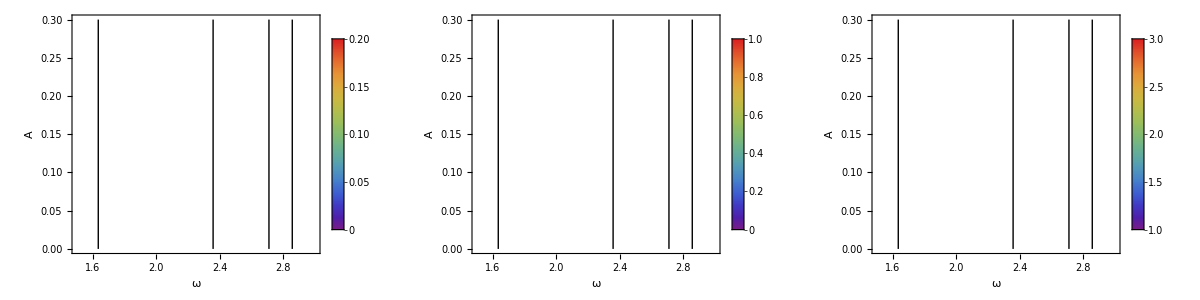

plots/benchmark.pdf

```mathematica
p2=Grid[{{rasterizeBackground[Show[ListDensityPlot[rates[[All,{2,3,5}]],InterpolationOrder->0,ImageSize->300,LabelStyle->Directive[16,Black],PlotRange->{0,0.2},ColorFunctionScaling->False,ColorFunction->(ColorData["Rainbow"][#/0.2]&), FrameLabel->{{A,None},{ω,"Growth Rate"}},ClippingStyle->None],PlotRangeClipping->None,Epilog->{Inset[BarLegend[{"Rainbow",{0,0.2}},LabelStyle->Directive[16,Black]],Scaled[{1.2,0.5}]],Line[{{#,0},{#,0.3}}]&/@Cases[(2*(modes*Tanh[modes])^(1/2)),u_/;u<3]},ImageSize->400,ImagePadding->{{65,100},{50,50}}]],rasterizeBackground[Show[ListDensityPlot[ReplacePart[rates[[All,{2,3,4}]],Position[rates[[All,{2,3,5}]],u_/;u<0]->-1],InterpolationOrder->0,ImageSize->300,LabelStyle->Directive[16,Black],ColorFunctionScaling->False,ColorFunction->(ColorData["Rainbow"][#/1]&),PlotRange->{0,1.1},ClippingStyle->None, FrameLabel->{{A,None},{ω,"Frequency"}}],PlotRangeClipping->None,Epilog->{Inset[BarLegend[{"Rainbow",{0,1}},LabelStyle->Directive[16,Black]],Scaled[{1.2,0.5}]],Line[{{#,0},{#,0.3}}]&/@Cases[(2*(modes*Tanh[modes])^(1/2)),u_/;u<3]},ImageSize->400,ImagePadding->{{65,100},{50,50}}]],rasterizeBackground[Show[ListDensityPlot[ReplacePart[rates[[All,{2,3,1}]],Position[rates[[All,{2,3,5}]],u_/;u<0]->-1],InterpolationOrder->0,ImageSize->300,LabelStyle->Directive[16,Black],ColorFunctionScaling->False,ColorFunction->(ColorData["Rainbow"][(#-1)/2]&),PlotRange->{0.9,3.1}, ClippingStyle->None,FrameLabel->{{A,None},{ω,"Wave Number"}}],PlotRangeClipping->None,Epilog->{Inset[BarLegend[{"Rainbow",{1,3}},LabelStyle->Directive[16,Black]],Scaled[{1.2,0.5}]],Line[{{#,0},{#,0.3}}]&/@Cases[(2*(modes*Tanh[modes])^(1/2)),u_/;u<3]},ImageSize->400,ImagePadding->{{65,100},{50,50}}]]}}]
p=Grid[{{p1},{p2}}];
Export["plots/benchmark.pdf",p]
```

## Generate random narrow peaks

{1.5708,3.14159}

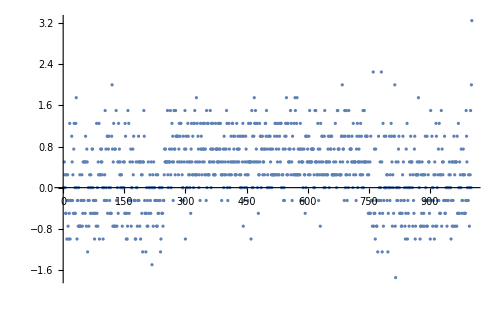

{1003,781,761,1002,814,685,120,872,574,569}

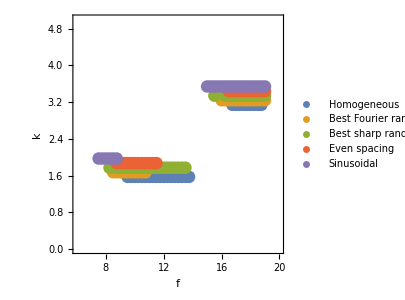

{0.,3.25,2.,2.25,-1.}

```mathematica
filebase="sweeps/sharp";
random=Table[If[FileExistsQ[filebase<>"/params"<>ToString[i]<>".txt"],Internal`StringToDouble/@#&/@DeleteCases[StringSplit/@StringSplit[Import[filebase<>"/params"<>ToString[i]<>".txt"],"\n"],{}],{}],{i,1,1003}];
seeds=Flatten[DeleteDuplicates/@random[[All,All,7]]];
wavenumbers=Sort[DeleteDuplicates[Flatten[(Cases[#,u_/;u[[4]]>0.0&&u[[3]]<0.6]&/@random)[[All,All,5]]]]]
mins[case_]:=Min/@(Cases[#,u_/;u[[4]]>0.0&&u[[3]]<0.6&&u[[5]]==case]&/@random)[[All,All,1]]
maxes[case_]:=Max/@(Cases[#,u_/;u[[4]]>0.0&&u[[3]]<0.6&&u[[5]]==case]&/@random)[[All,All,1]]
gaps=(mins/@wavenumbers[[2;;-1]])-(maxes/@wavenumbers[[1;;-2]]);
shifts=Transpose[#-gaps[[All,1001]]&/@(Transpose[gaps])];
ListPlot[shifts,ImageSize->500,PlotRange->All]
Reverse[Ordering[Join[shifts[[1,All]]]/.∞->0]][[1;;10]]
m1=781;
m2=300;
ListPlot[{{#[[1]],#[[2]]}&/@Cases[random[[1001]],u_/;u[[4]]>0.0&&u[[3]]<0.6][[All,{1,5}]],{#[[1]],#[[2]]+0.1}&/@Cases[random[[m1]],u_/;u[[4]]>0.0&&u[[3]]<0.6][[All,{1,5}]],{#[[1]],#[[2]]+0.2}&/@Cases[random[[m2]],u_/;u[[4]]>0.0&&u[[3]]<0.6][[All,{1,5}]],{#[[1]],#[[2]]+0.3}&/@Cases[random[[1002]],u_/;u[[4]]>0.0&&u[[3]]<0.6][[All,{1,5}]],{#[[1]],#[[2]]+0.4}&/@Cases[random[[1003]],u_/;u[[4]]>0.0&&u[[3]]<0.6][[All,{1,5}]]},PlotRange->{{6,20},{0,5}},ImageSize->300,Axes->False,Frame->True,FrameLabel->{"f","k"},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[1]],AspectRatio->1,PlotStyle->Directive[PointSize[0.03]],PlotLegends->{"Homogeneous","Best Fourier random","Best sharp random","Even spacing","Sinusoidal"}]
shifts[[1,{1001,1003,1002,m1,m2}]]
```

```mathematica
Cases[Ordering[Join[shifts[[1,All]]]/.∞->0],u_/;u>250&&u<750][[1;;10]]
```

{300,461,442,631,313,479,594,749,270,290}

```mathematica
shifts[[1,574]]
shifts[[1,300]]
shifts[[1,569]]
shifts[[1,781]]
```

1.75

-1.

1.75

2.25

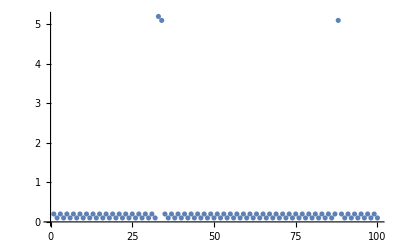

{1,54,45}

```mathematica
M=100;
{{Ms},ssin,scos}=Import["sweeps/sharp/300/substrate.dat"];
h0=Table[Sum[ssin[[i]]*Sin[Pi*(i-1)*(j-1)/M]+scos[[i]]*Cos[Pi*(i-1)*(j-1)/M],{i,1,Ms}],{j,1,M}];
ListPlot[h0,PlotRange->All]
{#[[1]],#[[2]],100-#[[1]]-#[[2]]}&@Differences[First/@Position[h0,u_/;u>Mean[h0]*2]]
```

```mathematica
M=100;
num=3;
Monitor[Do[bottom=ConstantArray[0,M];
indices=RandomInteger[{2,M-1},num];
bottom[[indices]]=bottom[[indices]]+ConstantArray[1.0,num];
c=Re[Fourier[bottom]];
s=Im[Fourier[bottom]];
If[!DirectoryQ["data/sharp/"<>ToString[j]],CreateDirectory["data/sharp/"<>ToString[j]]];
file=OpenWrite["data/sharp/"<>ToString[j]<>"/substrate.dat"];
WriteLine[file,M];
Do[WriteString[file,ToString[i,FortranForm]<>" "],{i,Riffle[s,ConstantArray[0.,M]]}];
WriteLine[file,""];
Do[WriteString[file,ToString[i,FortranForm]<>" "],{i,Riffle[c,ConstantArray[0.,M]]}];
WriteLine[file,""];
Close[file];,{j,1,500}],j];
bottom=ConstantArray[0,M];
indices=Table[Round[i],{i,M/6,M,M/3}];
bottom[[indices]]=bottom[[indices]]+ConstantArray[1.0,3];
c=Re[Fourier[bottom]];
s=Im[Fourier[bottom]];
If[!DirectoryQ["data/sharp/"<>ToString[0]],CreateDirectory["data/sharp/"<>ToString[0]]];
file=OpenWrite["data/sharp/"<>ToString[0]<>"/substrate.dat"];
WriteLine[file,M];
Do[WriteString[file,ToString[i,FortranForm]<>" "],{i,Riffle[s,ConstantArray[0.,M]]}];
WriteLine[file,""];
Do[WriteString[file,ToString[i,FortranForm]<>" "],{i,Riffle[c,ConstantArray[0.,M]]}];
WriteLine[file,""];
Close[file];
If[!DirectoryQ["data/sharp/"<>ToString[-1]],CreateDirectory["data/sharp/"<>ToString[-1]]];
file=OpenWrite["data/sharp/"<>ToString[-1]<>"/substrate.dat"];
WriteLine[file,M];
Do[WriteString[file,ToString[i,FortranForm]<>" "],{i,Riffle[s,ConstantArray[0.,M]]}];
WriteLine[file,""];
Do[WriteString[file,ToString[i,FortranForm]<>" "],{i,Riffle[c,ConstantArray[0.,M]]}];
WriteLine[file,""];
Close[file];
```

## Periodic gap and sharp plots

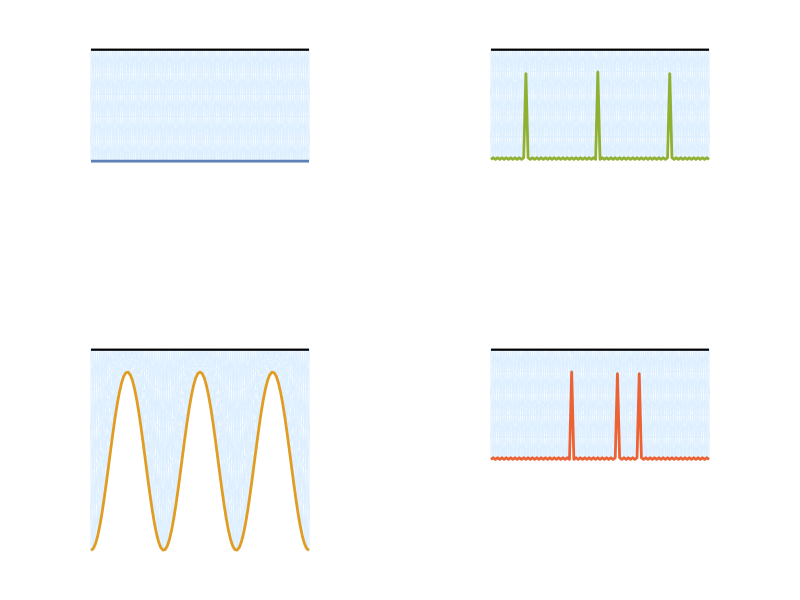

```mathematica
height=0.5;
length=4;
cols={ColorData[97,"ColorList"][[1]],ColorData[97,"ColorList"][[2]],ColorData[97,"ColorList"][[3]],ColorData[97,"ColorList"][[4]]};
filebases={"data/sharp1001","data/sharp1003","data/sharp502","data/sharp574"};
p0=Grid@Transpose@Partition[Table[filebase=filebases[[i]];
lst=StringSplit[Import[filebase<>".txt"],"\n"];
meshpoints=ToExpression[lst[[FirstPosition[lst,"Mesh points"][[1]]+1]]];
mesh=Partition[Partition[BinaryReadList[filebase<>".npy","Real64"][[1+(10+BinaryReadList[filebase<>".npy","Integer16"][[5]])*8/64;;-1]],2],meshpoints];
top=1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Surface points coordinates"][[1]]+1]]]];
bottom=1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Substrate points coordinates"][[1]]+1]]]];
con=Partition[1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Mesh cells"][[1]]+1]]," "]],3];
sides=Flatten[Position[mesh[[-1]],u_/;Length[u]>0&&(Abs[(u[[1]]^2)^(1/2)-length]<10^-6||Abs[(u[[1]]^2)^(1/2)]<10^-6)]];
m=Length[mesh];
mesh2=mesh[[m]];
Show[ListPlot[{mesh2[[top]]}, PlotStyle->Directive[Black], Joined->True,ImageSize->300,Axes->False,Frame->False,Prolog->{White,EdgeForm[LightBlue],Triangle[{mesh2[[#[[1]]]],mesh2[[#[[2]]]],mesh2[[#[[3]]]]}]&/@con},AspectRatio->(1.1)/(length+2),PlotRange->{{-1,length+1},{-0.5,0.6}}],ListPlot[mesh2[[bottom]],Joined->True,PlotStyle->{Directive[cols[[i]],AbsoluteThickness[2]]},PlotRange->All]],{i,1,Length[filebases]}],2]
```

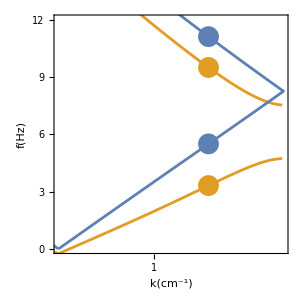

```mathematica
height=0.5;
length=4.0;
gap=2*Pi/length*3/2;
ks=2*gap;
hs=0.45;
M2=3;
κ[k_, n_]:=k+n*ks;
ν1=2;
ν3=0.1;
g=980;
σ=72;
ρ=1;
H1[k_,A_]:=Table[Exp[-κ[k,n]*height]*(g+σ/ρ*κ[k,n]^2)*κ[k,n]*(BesselJ[m-n,-I*κ[k,n]*A]-I/2*ks*A*BesselJ[m-n-1,-I*κ[k,n]*A]-I/2*ks*A*BesselJ[m-n+1,-I*κ[k,n]*A])-Exp[κ[k,n]*height]*(g+σ/ρ*κ[k,n]^2)*κ[k,n]*(BesselJ[m-n,I*κ[k,n]*A]+I/2*ks*A*BesselJ[m-n-1,I*κ[k,n]*A]+I/2*ks*A*BesselJ[m-n+1,I*κ[k,n]*A]),{n,-M2,M2},{m,-M2,M2}];
H2[k_,A_]:=-Table[Exp[-κ[k,n]*height]*(BesselJ[m-n,-I*κ[k,n]*A]-I/2*ks*A*BesselJ[m-n-1,-I*κ[k,n]*A]-I/2*ks*A*BesselJ[m-n+1,-I*κ[k,n]*A])+Exp[κ[k,n]*height]*(BesselJ[m-n,I*κ[k,n]*A]+I/2*ks*A*BesselJ[m-n-1,I*κ[k,n]*A]+I/2*ks*A*BesselJ[m-n+1,I*κ[k,n]*A]),{n,-M2,M2},{m,-M2,M2}];
H3[k_,A_]:=Table[1.0/Cosh[κ[k,n]*height]*KroneckerDelta[n,m],{n,-M2,M2},{m,-M2,M2}];
sys[k_,A_]:={H3[k,A].H1[k,A],H3[k,A].H2[k,A]};
p1=Show[Show[ListPlot[Transpose[Table[{k,#^(1/2)/(2*Pi)-0.25}&/@SingularValueList[sys[k,hs]][[-3;;-1]],{k,2*Pi/length,6*Pi/length,2*Pi/length}]],Joined->False,Axes->False,Frame->True,LabelStyle->Directive[16],PlotRange->{{-gap,gap},{0,12}},FrameTicks->{{Table[{i,i},{i,0,12,3}],Table[{i,""},{i,0,12,3}]},{Table[{i,i},{i,-3,3,1}],Table[{i,""},{i,-3,3,1}]}},FrameLabel->{DisplayForm[RowBox[{k,"(",Superscript["cm",-1],")"}]],DisplayForm[RowBox[{f,"(Hz)"}]]},FrameStyle->Directive[Black,AbsoluteThickness[2]],AspectRatio->1,ImageSize->300,ImagePadding->{{65,10},{65,10}},LabelStyle->Directive[16],PlotStyle->Directive[PointSize[0.05],ColorData[97,"ColorList"][[2]]]],ListPlot[Transpose[Table[{k,#^(1/2)/(2*Pi)-0.25}&/@SingularValueList[sys[k,hs]][[-3;;-1]],{k,-2*Pi/length,-6*Pi/length,-2*Pi/length}]],Joined->False,PlotStyle->Directive[PointSize[0.05],ColorData[97,"ColorList"][[2]]]],ListPlot[Transpose[Table[{k,#^(1/2)/(2*Pi)-0.25}&/@SingularValueList[sys[k,hs]][[-3;;-1]],{k,-ks/2+0.01,ks/2-0.01,ks/200}]],Joined->True,PlotStyle->Directive[AbsoluteThickness[2],ColorData[97,"ColorList"][[2]]]]],Show[ListPlot[{Table[{If[k<gap,k,If[k<3*gap,2*gap-k,k-4*gap]],(g*k*Tanh[k*height]*(1+σ/g*k^2))^(1/2)/(2*Pi)},{k,2*Pi/length,6*Pi/length,2*Pi/length}],Table[{-If[k<gap,k,If[k<3*gap,2*gap-k,k-4*gap]],(g*k*Tanh[k*height]*(1+σ/g*k^2))^(1/2)/(2*Pi)},{k,2*Pi/length,6*Pi/length,2*Pi/length}]},Joined->False,PlotStyle->Directive[ColorData[97,"ColorList"][[1]],PointSize[0.05]]],ListPlot[{Table[{If[k<gap,k,If[k<3*gap,2*gap-k,k-4*gap]],(g*k*Tanh[k*height]*(1+σ/g*k^2))^(1/2)/(2*Pi)},{k,0,6*Pi/length,Pi/length/50}],Table[{-If[k<gap,k,If[k<3*gap,2*gap-k,k-4*gap]],(g*k*Tanh[k*height]*(1+σ/g*k^2))^(1/2)/(2*Pi)},{k,0,6*Pi/length,Pi/length/50}]},Joined->True,PlotStyle->Directive[ColorData[97,"ColorList"][[1]],AbsoluteThickness[2.0]]]],PlotRange->{{0,gap},{0,12}}]
```

```mathematica
2*Pi/ks
4/(2*Pi/ks)
```

1.33333

3.

```mathematica
ks/(2*Pi)
```

0.75

{4.14821,Null}

{0.323272,Null}

{4.22437,Null}

{0.322006,Null}

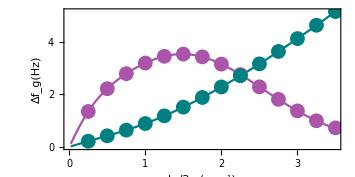

gapsize.pdf

```mathematica
length=4;
M2=3;
ks0=Pi/25;
ks1=7*Pi;
dks=Pi/25;
AbsoluteTiming[gaps1=Table[{ks/(2*Pi),(#[[2]]-#[[1]])&@(Sort[SingularValueList[sys[ks/2,hs]]][[1;;2]]^(1/2)/(2*Pi))},{ks,ks0,ks1,dks}];]
AbsoluteTiming[gaps2=Table[{ks/(2*Pi),(#[[2]]-#[[1]])&@(Sort[SingularValueList[sys[ks/2,hs]]][[1;;2]]^(1/2)/(2*Pi))},{ks,2*Pi/length,ks1,2*Pi/length}];]
AbsoluteTiming[gaps3=Table[{ks/(2*Pi),((#[[2]]+#[[1]])/2)&@(Sort[SingularValueList[sys[ks/2,hs]]][[1;;2]]^(1/2)/(2*Pi))},{ks,ks0,ks1,dks}];]
AbsoluteTiming[gaps4=Table[{ks/(2*Pi),((#[[2]]+#[[1]])/2)&@(Sort[SingularValueList[sys[ks/2,hs]]][[1;;2]]^(1/2)/(2*Pi))},{ks,2*Pi/length,ks1,2*Pi/length}];]

scale1=5;
scale2=50;
p4=Show[ListPlot[{{#[[1]],#[[2]]/scale1}&/@gaps1,{#[[1]],#[[2]]/scale2}&/@gaps3},Axes->False,Frame->True,FrameLabel->{{Style[DisplayForm[RowBox[{Subscript[Δf,"g"], "(Hz)"}]],Lighter[Purple]],Style[DisplayForm[RowBox[{OverBar[Subscript[f,"g"]], "(Hz)"}]],RGBColor[{0,1/2,1/2}]]},{DisplayForm[RowBox[{Subscript[k,s],"/",2*Pi,"(",Superscript["cm",-1],")"}]],None}},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[2]],Joined->True,PlotStyle->{Directive[Lighter[Purple]],Directive[RGBColor[{0,1/2,1/2}]]},ImageSize->300,FrameTicks->{{Table[{i/scale1,Style[PaddedForm[i,{2,1}],Lighter[Purple]]},{i,0,scale1,scale1/5}],Table[{i/scale2,Style[i,RGBColor[{0,1/2,1/2}]]},{i,0,scale2,scale2/5}]},{Table[{i,i},{i,0,ks1/(2*Pi),1}],Table[{i,""},{i,0,3,0.5}]}}],ListPlot[{{#[[1]],#[[2]]/scale1}&/@gaps2,{#[[1]],#[[2]]/scale2}&/@gaps4},Joined->False,PlotStyle->{Directive[PointSize[0.03],Lighter[Purple]],Directive[PointSize[0.03],RGBColor[{0,1/2,1/2}]]}],ImageSize->355,ImagePadding->{{65,65},{65,10}},AspectRatio->1/2]
Export["gapsize.pdf",p4]
```

```mathematica
BarLegend[{"TemperatureMap",{0,1}}]
```

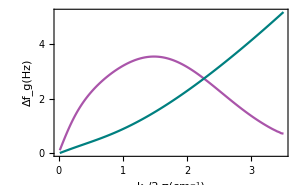

```mathematica
ListPlot[{{#[[1]],#[[2]]/scale1}&/@gaps1,{#[[1]],#[[2]]/scale2}&/@gaps3},Axes->False,Frame->True,FrameLabel->{{Style[DisplayForm[RowBox[{Subscript[Δf,"g"], "(Hz)"}]],Lighter[Purple]],Style[DisplayForm[RowBox[{OverBar[Subscript[f,"g"]], "(Hz)"}]],RGBColor[{0,1/2,1/2}]]},{DisplayForm[RowBox[{Subscript[k,s],"/",2*Pi,"(",Superscript["cm",-1],")"}]],None}},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[2]],Joined->True,PlotStyle->{Directive[Lighter[Purple]],Directive[RGBColor[{0,1/2,1/2}]]},ImageSize->300,FrameTicks->{{Table[{i/scale1,Style[PaddedForm[i,{2,1}],Lighter[Purple]]},{i,0,scale1,scale1/5}],Table[{i/scale2,Style[i,RGBColor[{0,1/2,1/2}]]},{i,0,scale2,scale2/5}]},{Table[{i,i},{i,0,ks1/(2*Pi),1}],Table[{i,""},{i,0,3,0.5}]}}]
```

{3.93318,Null}

{0.314086,Null}

{3.93779,Null}

{0.311319,Null}

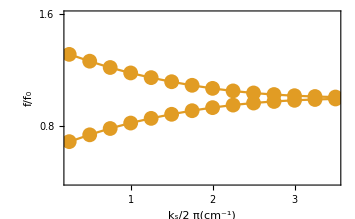

```mathematica
length=4;
M2=3;
ks0=Pi/25;
ks1=7*Pi;
dks=Pi/25;
AbsoluteTiming[gaps1=Table[{ks/(2*Pi),2*#[[1]]/(#[[1]]+#[[2]])&@(Sort[SingularValueList[sys[ks/2,hs]]][[1;;2]]^(1/2)/(2*Pi))},{ks,ks0,ks1,dks}];]
AbsoluteTiming[gaps2=Table[{ks/(2*Pi),2*#[[1]]/(#[[1]]+#[[2]])&@(Sort[SingularValueList[sys[ks/2,hs]]][[1;;2]]^(1/2)/(2*Pi))},{ks,2*Pi/length,ks1,2*Pi/length}];]
AbsoluteTiming[gaps3=Table[{ks/(2*Pi),2*#[[2]]/(#[[1]]+#[[2]])&@(Sort[SingularValueList[sys[ks/2,hs]]][[1;;2]]^(1/2)/(2*Pi))},{ks,ks0,ks1,dks}];]
AbsoluteTiming[gaps4=Table[{ks/(2*Pi),2*#[[2]]/(#[[1]]+#[[2]])&@(Sort[SingularValueList[sys[ks/2,hs]]][[1;;2]]^(1/2)/(2*Pi))},{ks,2*Pi/length,ks1,2*Pi/length}];]

scale1=2.0;
p4=Show[ListPlot[{{#[[1]],#[[2]]}&/@gaps1,{#[[1]],#[[2]]}&/@gaps3},Axes->False,Frame->True,PlotRange->{{1/length,ks1/(2*Pi)},{0.4,1.6}},FrameLabel->{{DisplayForm[RowBox[{f, "/",Subscript[f,0]}]],None},{DisplayForm[RowBox[{Subscript[k,s],"/",2*Pi,"(",Superscript["cm",-1],")"}]],None}},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[2]],Joined->True,PlotStyle->Directive[ColorData[97,"ColorList"][[2]]],ImageSize->300,FrameTicks->{{Table[{i,PaddedForm[i,{2,1}]},{i,0,scale1,scale1/5}],Table[{i,""},{i,0,scale1,scale1/5}]},{Table[{i,i},{i,0,ks1/(2*Pi),1}],Table[{i,""},{i,0,3,0.5}]}}],ListPlot[{{#[[1]],#[[2]]}&/@gaps2,{#[[1]],#[[2]]}&/@gaps4},Joined->False,PlotStyle->Directive[PointSize[0.03],ColorData[97,"ColorList"][[2]]]],ImageSize->355,ImagePadding->{{65,65},{65,10}}]
```

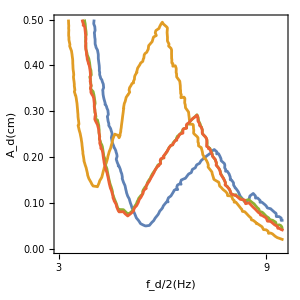

```mathematica
filebases={"sweeps/sharpamp/1001","sweeps/sharpamp/1003","sweeps/sharpamp/1002","sweeps/sharpamp/574"};
cols={ColorData[97,"ColorList"][[1]],ColorData[97,"ColorList"][[2]],ColorData[97,"ColorList"][[3]],ColorData[97,"ColorList"][[4]]};
sweeps=Flatten[Table[If[FileExistsQ[#<>"/params"<>ToString[i]<>".txt"],Internal`StringToDouble/@#&/@DeleteCases[StringSplit/@StringSplit[Import[#<>"/params"<>ToString[i]<>".txt"],"\n"],{}],{}],{i,1,100}],1]&/@filebases;
p2=Show@@Table[ListContourPlot[{#[[1]]/2,#[[2]]/(2*Pi*#[[1]])^2*980,#[[3]]}&/@sweeps[[i,All,{1,2,4}]],Contours->{0.5},PlotRange->{{3,9.5},{0,0.5}},ContourShading->None,ContourStyle->{Directive[cols[[i]],Opacity[1],AbsoluteThickness[2]]},LabelStyle->Directive[16,Black], FrameLabel->{{DisplayForm[RowBox[{HoldForm[Subscript[A,d]],"(cm)"}]],None},{DisplayForm[RowBox[{Subscript[f,d],"/",2,"(Hz)"}]],None}},FrameStyle->Directive[Black,AbsoluteThickness[2.0]],ImageSize->300,ImagePadding->{{65,10},{65,10}},FrameTicks->{{Table[{i,PaddedForm[i,{2,2}]},{i,0,0.5,0.1}],Table[{i,""},{i,0,0.5,0.1}]},{Table[{i,i},{i,3,16,3}],Table[{i,""},{i,3,16,3}]}}],{i,1,Length[sweeps]}]
```

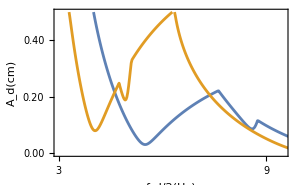

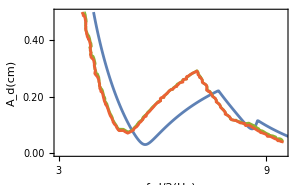

```mathematica
filebases={"sweeps/sharpamp/1002","sweeps/sharpamp/574"};
flatfloquet=Import["data/flatfloquet.txt","Table"];
periodicfloquet=Import["data/periodicfloquet.txt","Table"];
cols={ColorData[97,"ColorList"][[3]],ColorData[97,"ColorList"][[4]]};
sweeps=Flatten[Table[If[FileExistsQ[#<>"/params"<>ToString[i]<>".txt"],Internal`StringToDouble/@#&/@DeleteCases[StringSplit/@StringSplit[Import[#<>"/params"<>ToString[i]<>".txt"],"\n"],{}],{}],{i,1,100}],1]&/@filebases;
p2=Show[ListPlot[{flatfloquet,periodicfloquet},PlotRange->{{3,9.5},{0,0.5}},LabelStyle->Directive[16,Black], Joined->True,Axes->False,Frame->True,PlotStyle->Directive[AbsoluteThickness[2]],FrameLabel->{{DisplayForm[RowBox[{HoldForm[Subscript[A,d]],"(cm)"}]],None},{DisplayForm[RowBox[{Subscript[f,d],"/",2,"(Hz)"}]],None}},FrameStyle->Directive[Black,AbsoluteThickness[2.0]],ImageSize->300,ImagePadding->{{65,10},{65,10}},FrameTicks->{{Table[{i,PaddedForm[i,{2,2}]},{i,0,0.5,0.1}],Table[{i,""},{i,0,0.5,0.1}]},{Table[{i,i},{i,3,16,3}],Table[{i,""},{i,3,16,3}]}}]]
p3=Show[ListPlot[{flatfloquet},PlotRange->{{3,9.5},{0,0.5}},LabelStyle->Directive[16,Black], Joined->True,Axes->False,Frame->True,PlotStyle->Directive[AbsoluteThickness[2]],FrameLabel->{{DisplayForm[RowBox[{HoldForm[Subscript[A,d]],"(cm)"}]],None},{DisplayForm[RowBox[{Subscript[f,d],"/",2,"(Hz)"}]],None}},FrameStyle->Directive[Black,AbsoluteThickness[2.0]],ImageSize->300,ImagePadding->{{65,10},{65,10}},FrameTicks->{{Table[{i,PaddedForm[i,{2,2}]},{i,0,0.5,0.1}],Table[{i,""},{i,0,0.5,0.1}]},{Table[{i,i},{i,3,16,3}],Table[{i,""},{i,3,16,3}]}}],Show@@Table[ListContourPlot[{#[[1]]/2,#[[2]]/(2*Pi*#[[1]])^2*980,#[[3]]}&/@sweeps[[i,All,{1,2,4}]],Contours->{0.5},PlotRange->{{3,9.5},{0,0.5}},ContourShading->None,ContourStyle->{Directive[cols[[i]],Opacity[1],AbsoluteThickness[2]]},LabelStyle->Directive[16,Black], FrameLabel->{{DisplayForm[RowBox[{HoldForm[Subscript[A,d]],"(cm)"}]],None},{DisplayForm[RowBox[{Subscript[f,d],"/",2,"(Hz)"}]],None}},FrameStyle->Directive[Black,AbsoluteThickness[2.0]],ImageSize->300,ImagePadding->{{65,10},{65,10}},FrameTicks->{{Table[{i,PaddedForm[i,{2,2}]},{i,0,0.5,0.1}],Table[{i,""},{i,0,0.5,0.1}]},{Table[{i,i},{i,3,16,3}],Table[{i,""},{i,3,16,3}]}}],{i,1,Length[sweeps]}],FrameLabel->{{DisplayForm[RowBox[{HoldForm[Subscript[A,d]],"(cm)"}]],None},{DisplayForm[RowBox[{Subscript[f,d],"/",2,"(Hz)"}]],None}},FrameStyle->Directive[Black,AbsoluteThickness[2.0]],ImageSize->300,ImagePadding->{{65,10},{65,10}},FrameTicks->{{Table[{i,PaddedForm[i,{2,2}]},{i,0,0.5,0.1}],Table[{i,""},{i,0,0.5,0.1}]},{Table[{i,i},{i,3,16,3}],Table[{i,""},{i,3,16,3}]}}]
```

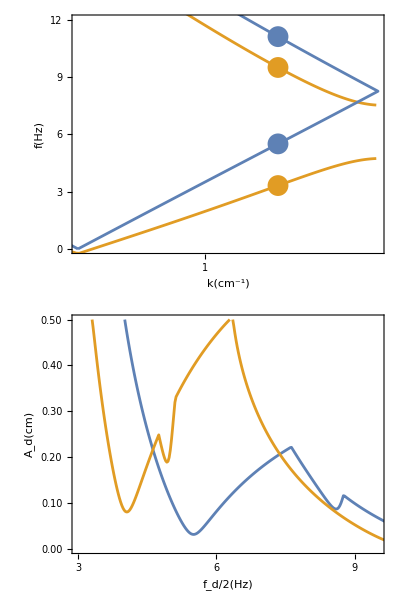
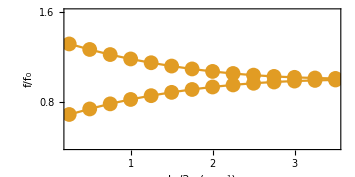
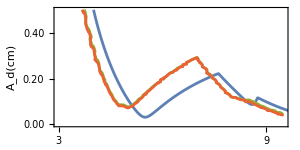
-Graphics- | -Graphics- | -Graphics- | -Graphics-

plots/sharpsubstrates.pdf

```mathematica
p=Grid[{{p0,Grid[{{Show[p1,AspectRatio->1/2]},{Show[p2,AspectRatio->1/2]}}],Show[p4,AspectRatio->1/2],Show[p3,AspectRatio->1/2]}}]
Export["plots/sharpsubstrates.pdf",p]
```